# Play around with replace

## Load data

```mathematica
<<HokahokaW`
```

HokahokaW`
Git HEAD hash loaded on Mon 11 May 2015 20:18:03 is dfc276416b3fda60a30e53692c8c82eaed59709c.
Remember that this is at latest the penultimate commit before deployment. You should use a live git repo if possible, for better version tracking.

```mathematica
testFileName=ParentDirectory[NotebookDirectory[]]<>"\\_resources\\tDC004_150313_120455.pp2rl.tsv"
```

C:\prog\_lab\pyonpyon\pyonpyonw\Tests\_resources\tDC004_150313_120455.pp2rl.tsv

```mathematica
testData=Import[testFileName];
```

## PP2SplitTrialImpl Tests

```mathematica
(*Extract all state 4 logs, which mark the loading of a trial*)
tempSequenceStarts=SequenceCases[
Select[testData,#[[1]]=="STATE"&] (*First, filter out all the "TRIAL" and "ERROR" lines*),
 {{"STATE", _, _,_,_,4, ___},{"STATE", trialNumber_, timeStamp_,_,_,x_/;MemberQ[{5,8,11},x], ___}}:> {trialNumber,timeStamp}
]
```

{{0,187085},{1,217285},{2,243944},{3,277405},{4,310817},{5,349360},{6,379349},{7,408335},{8,436915},{9,464933},{10,498040},{11,528632},{12,556951},{13,590102},{14,618526},{15,652525},{16,685156},{17,711739},{18,741739},{19,765911},{20,799252},{21,824876},{22,854252},{23,877156},{24,907783},{25,932348},{26,957508},{27,986893},{28,1016281},{29,1043999},{30,1077829},{31,1102067},{32,1129405},{33,1157753},{34,1191508},{35,1226407},{36,1250012},{37,1286267},{38,1318034},{39,1349077},{40,1381910},{41,1407829},{42,1429831},{43,1456492},{44,1486889},{45,1515334},{46,1547009},{47,1576663},{48,1612672},{49,1644727},{50,1671379},{51,1697935},{52,1725928},{53,1754212},{54,1783651},{55,1810586},{56,1839554},{57,1872143},{58,1902355},{59,1933720}}

```mathematica
tempSequenceStarts[[All, 1]]==Range[0,59] (*Check to make sure that all trials were extracted*)
```

True

```mathematica
PP2SplitTrialImpl[dataTable_,trial_]:=
Module[{},
Replace[
dataTable, 
{___,
entryStart:{"STATE", trial, ___},
Longest[contents___],
entryLast:{"STATE",   trial, ___},
rest___}  :>{{entryStart,contents,entryLast}, {rest}}
]
(*Select[tempTrials,(#[[1]]=="STATE" || #[[1]]=="TRIAL")&]*)
]
```

```mathematica
PP2SplitTrialImpl[testData, 58]
```

{{{STATE,58,1896235,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    50},{STATE,58,1896285,50,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{ERROR,99999,Run loop diff is >25 ms:    64},{STATE,58,1901351,64,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,58,1902355,2,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,58,1903908,5,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,58,1903924,16,1,6,FALSE,FALSE,TRUE,FALSE,354,1555,0},{STATE,58,1903928,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1555,0},{STATE,58,1903939,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1555,0},{STATE,58,1914791,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1555,0}},{{STATE,59,1927618,8,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.},{ERROR,99999,Run loop diff is >25 ms:    28},{STATE,59,1927646,28,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{ERROR,99999,Run loop diff is >25 ms:    70},{STATE,59,1932717,70,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{ERROR,99999,Run loop diff is >25 ms:    29},{STATE,59,1933720,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,59,1935985,3,2,8,FALSE,FALSE,TRUE,FALSE,642,0,0},{STATE,59,1935991,6,2,9,FALSE,FALSE,TRUE,TRUE,659,2268,0},{STATE,59,1938907,3,2,9,FALSE,TRUE,TRUE,TRUE,663,2268,0},{STATE,59,1938913,6,2,14,FALSE,TRUE,TRUE,FALSE,742,2268,2922},{STATE,59,1938922,9,2,14,FALSE,TRUE,FALSE,FALSE,740,2268,2922},{STATE,59,1955971,3,2,14,FALSE,FALSE,FALSE,FALSE,736,2268,2922},{STATE,60,1958113,17,2,15,FALSE,FALSE,FALSE,FALSE,752,0,0},{STATE,60,1967155,3,2,15,FALSE,TRUE,FALSE,FALSE,756,0,0},{RUNLOG END,15.03.13_12:37:48}}}

## PP2SplitTrial

```mathematica
(*Implementation copied from previous section*)
PP2SplitTrialImpl[dataTable_,trial_]:=
Module[{},
Replace[
dataTable, 
{___,
entryStart:{"STATE", trial, ___},
Longest[contents___],
entryLast:{"STATE",   trial, ___},
rest___}  :>{{entryStart,contents,entryLast}, {rest}}
]
(*Select[tempTrials,(#[[1]]=="STATE" || #[[1]]=="TRIAL")&]*)
];
```

```mathematica
PP2SplitTrial[dataTable_]:=
Module[{tempTrial, tempRest},
tempRest=dataTable;
Table[
{tempTrial,tempRest}=PP2SplitTrialImpl[tempRest, n];
<| "TrialNumber"-> n+1,
"STATEDATA"-> Select[tempTrial, #[[1]]=="STATE"&],
"ERRORDATA"-> Select[tempTrial, #[[1]]=="ERROR"&],
"TRIALDATA"-> Select[tempTrial, #[[1]]=="TRIAL"& ]|>,
{n, 0, 59}]
]
```

```mathematica
testDataTrials=PP2SplitTrial[testData];
```

```mathematica
testDataTrials[[3]]
```

<|TrialNumber→3,STATEDATA→{{STATE,2,237824,3,1,2,FALSE,TRUE,FALSE,FALSE,292,0,0},{STATE,2,237872,48,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,2,242941,69,1,4,FALSE,TRUE,FALSE,FALSE,324,0,0},{STATE,2,243944,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,2,245003,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,2,245011,8,1,6,FALSE,FALSE,TRUE,FALSE,354,1062,0},{STATE,2,245015,4,1,14,FALSE,FALSE,TRUE,FALSE,482,1062,0},{STATE,2,245026,11,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0},{STATE,2,249728,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1062,0},{STATE,2,266035,3,1,14,FALSE,FALSE,FALSE,FALSE,480,1062,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    48},{ERROR,99999,Run loop diff is >25 ms:    69},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}|>

```mathematica
testDataTrials[[4]]
```

<|TrialNumber→4,STATEDATA→{{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    55},{ERROR,99999,Run loop diff is >25 ms:    38},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.}}|>

```mathematica
testDataTrials[[7]]
```

<|TrialNumber→7,STATEDATA→{{STATE,6,372431,3,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{STATE,6,372500,69,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,6,373304,3,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,6,378346,38,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{STATE,6,379349,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,6,381341,3,1,5,FALSE,TRUE,TRUE,FALSE,342,0,0},{STATE,6,381347,6,1,6,FALSE,TRUE,TRUE,FALSE,358,1995,0},{STATE,6,381351,4,1,14,FALSE,TRUE,TRUE,FALSE,486,1995,0},{STATE,6,381361,10,1,14,FALSE,TRUE,FALSE,FALSE,484,1995,0},{STATE,6,389729,4,1,14,FALSE,FALSE,FALSE,FALSE,480,1995,0},{STATE,6,395192,3,1,14,FALSE,TRUE,FALSE,FALSE,484,1995,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    69},{ERROR,99999,Run loop diff is >25 ms:    38},{ERROR,99999,Run loop diff is >25 ms:    30}},TRIALDATA→{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}|>

```mathematica
(*Checks that all trials from 1 to 60 were extracted*)
testDataTrials[[All, "TrialNumber"]] == Range[1,60]
```

True

## Extracting trial type: PP2TrialType(*/PP2TrialTypeList*)

### Playing around

```mathematica
testDataTrials[[3, "TRIALDATA"]]
```

{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}

```mathematica
Cases[testDataTrials[[3, "TRIALDATA"]], {"TRIAL",___}]
```

{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}

```mathematica
Cases[testDataTrials[[4, "TRIALDATA"]], {"TRIAL",___}]
```

{{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.}}

```mathematica
Replace[ 2, {1 -> "GO", 2-> "NOGO",3->"TEST",  _->"Invalid!"} ]
```

NOGO

### Paste together into real function

```mathematica
PP2TrialExtractType[trialData_Association]:= 
Module[{tempret},
tempret=trialData[["TRIALDATA"]];
If[Length[tempret]≠1, 
Message[PP2TrialExtractType::trialError, trialData],
];
Replace[tempret[[1, 3]], {1 -> "GO", 2-> "NOGO",3->"TEST", _->"Invalid!"} ]
];
```

```mathematica
PP2TrialExtractType::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialExtractType[x___]:= Message[PP2TrialExtractType::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractType[testDataTrials[[3]]]
```

GO

```mathematica
PP2TrialExtractType[testDataTrials[[4]]]
```

NOGO

```mathematica
PP2TrialExtractType /@ testDataTrials
```

{GO,GO,GO,NOGO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO}

### Rewrite for more generality

```mathematica
PP2TrialExtractTrialDataImpl[trialData_Association, trialDataNumber_, replacementList_List]:= 
Module[{tempret},
tempret=trialData[["TRIALDATA"]];
If[Length[tempret]≠1, 
Message[PP2TrialExtractTrialDataImpl::trialError, trialData],
];
Replace[tempret[[1, trialDataNumber]],  replacementList]
];
```

```mathematica
PP2TrialExtractTrialDataImpl::trialError="Something is wrong with this trial!";
```

### Rewrite PP2TrialExtractType

```mathematica
PP2TrialExtractType[trialData_Association]:= PP2TrialExtractTrialDataImpl[trialData, 3,{1 -> "GO", 2-> "NOGO",3->"TEST", _->"Invalid!"}  ];
PP2TrialExtractType[x___]:= Message[PP2TrialExtractType::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractType[testDataTrials[[3]]]
```

GO

```mathematica
PP2TrialExtractType[testDataTrials[[4]]]
```

NOGO

```mathematica
PP2TrialExtractType /@ testDataTrials
```

{GO,GO,GO,NOGO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,NOGO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,NOGO,NOGO,GO,GO,NOGO,NOGO,GO,GO,NOGO,GO,NOGO,GO,NOGO,GO,GO,NOGO,GO,NOGO,GO,GO,NOGO,NOGO,GO,NOGO,GO,NOGO,GO,NOGO}

### PP2TrialExtractFootshockAmplitude, PP2TrialExtractCode

```mathematica
PP2TrialExtractCode[trialData_Association]:= PP2TrialExtractTrialDataImpl[trialData, 2,{}  ];
PP2TrialExtractCode[x___]:= Message[PP2TrialExtractCode::invalidArgs, x];
```

```mathematica
PP2TrialExtractFootshockAmplitude[trialData_Association]:= PP2TrialExtractTrialDataImpl[trialData, 5,{}  ];
PP2TrialExtractFootshockAmplitude[x___]:= Message[PP2TrialExtractFootshockAmplitude::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractCode /@ testDataTrials
```

{1,1,1,2,2,2,1,2,1,2,1,2,1,1,2,1,2,1,1,2,1,2,1,2,2,1,2,2,1,2,1,2,2,2,1,1,2,2,1,1,2,1,2,1,2,1,1,2,1,2,1,1,2,2,1,2,1,2,1,2}

```mathematica
PP2TrialExtractFootshockAmplitude /@ testDataTrials
```

{600.,600.,600.,120.,120.,120.,600.,120.,600.,120.,600.,120.,600.,600.,120.,600.,120.,600.,600.,120.,600.,120.,600.,120.,120.,600.,120.,120.,600.,120.,600.,120.,120.,120.,600.,600.,120.,120.,600.,600.,120.,600.,120.,600.,120.,600.,600.,120.,600.,120.,600.,600.,120.,120.,600.,120.,600.,120.,600.,120.}

## Extracting trial outcome:PP2TrialExtractOutcome(*/PP2TrialOutcomeList*)

### Playing around

```mathematica
testDataTrials[[4,"STATEDATA", All, 6]]
```

{2,3,3,4,8,10,14,14,14}

```mathematica
Intersection[%,{6,7,9,10,12,13}]
```

{10}

```mathematica
Replace[10, {6 -> "H", 7-> "M", 9->"FA", 10-> "CR",12->"TJ",13->"TT",_->"Invalid!"} ]
```

CR

### Paste together into real function

```mathematica
PP2TrialExtractOutcome[trialData_Association]:= 
Module[{tempret},
tempret=Intersection[trialData[["STATEDATA", All, 6]],{6,7,9,10,12,13}];
If[Length[tempret]≠1, 
Message[PP2TrialExtractType::trialError, trialData],
];
Replace[tempret[[1]], {6 -> "H", 7-> "M", 9->"FA", 10-> "CR",12->"TJ",13->"TT",_->"Invalid!"} ]
];
```

```mathematica
PP2TrialExtractOutcome::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialExtractOutcome[x___]:= Message[PP2TrialExtractOutcome::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialExtractOutcome[testDataTrials[[3]]]
```

H

```mathematica
PP2TrialExtractOutcome[testDataTrials[[4]]]
```

CR

```mathematica
PP2TrialExtractOutcome /@ testDataTrials
```

{M,H,H,CR,CR,CR,H,CR,H,FA,H,CR,M,H,CR,M,CR,H,H,FA,H,CR,H,FA,CR,M,CR,CR,H,CR,H,CR,CR,FA,H,H,FA,FA,H,M,CR,H,FA,M,CR,M,M,FA,H,CR,M,M,CR,CR,H,CR,M,CR,H,FA}

### Pie Chart

```mathematica
Tally[PP2TrialExtractOutcome /@ testDataTrials]
```

{{M,11},{H,19},{CR,21},{FA,9}}

```mathematica
SortBy[%, First][[{3,4,1,2}]]
```

{{H,19},{M,11},{CR,21},{FA,9}}

```mathematica
PP2TrialOutcomePieChart[dataTable_:{__Association}]:= 
Module[{tempTally},
tempTally = Tally[PP2TrialExtractOutcome /@ dataTable];
tempTally =SortBy[tempTally , First][[{3,4,1,2}]]; (*Sorting here makes sure that the pie wedges are in order, with correct coloring*)
PieChart[ tempTally[[All,2]], 
	ChartLabels-> tempTally[[All, 1]],
	ChartStyle-> {Darker[Green], Opacity[0.3,Darker[Green]], Opacity[0.3,Darker[Red]], Darker[Red]}
]
]
```

```mathematica
PP2TrialOutcomePieChart[x___]:= Message[PP2TrialOutcomePieChart::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialOutcomePieChart[testDataTrials]
```

-Graphics-

## Extracting trial outcome: PP2TrialExtractOutcome(*/PP2TrialOutcomeList*)

## Extracting trial latencies: PP2TrialResponseLatency(*/PP2TrialResponseLatencyList*)

```mathematica
testDataTrials[[4]]
```

<|TrialNumber→4,STATEDATA→{{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    55},{ERROR,99999,Run loop diff is >25 ms:    38},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,2,2,1,120.,250.,4,4000.,2000.,0.,0.}}|>

```mathematica
(*This way, you only have to deal with one trial worth of state annotations at a time!*)
```

```mathematica
testDataTrials[[4, "STATEDATA"]]
```

{{STATE,3,267065,3,1,2,FALSE,FALSE,FALSE,FALSE,288,0,0},{STATE,3,267120,55,2,3,FALSE,FALSE,FALSE,FALSE,560,0,0},{STATE,3,271360,3,2,3,FALSE,TRUE,FALSE,FALSE,564,0,0},{STATE,3,276400,38,2,4,FALSE,TRUE,FALSE,FALSE,580,0,0},{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0},{STATE,3,281425,11,2,14,FALSE,TRUE,TRUE,FALSE,742,0,0},{STATE,3,281435,10,2,14,FALSE,TRUE,FALSE,FALSE,740,0,0},{STATE,3,295748,3,2,14,FALSE,FALSE,FALSE,FALSE,736,0,0}}

```mathematica
SequenceCases[testDataTrials[[4, "STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{5,8,11}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{5,8,11,7,10,13}, state2],___ }
}
]
```

{{{STATE,3,277405,3,2,8,FALSE,TRUE,TRUE,FALSE,646,0,0},{STATE,3,281414,4,2,10,FALSE,TRUE,TRUE,FALSE,678,0,0}}}

### Paste together into real function

```mathematica
PP2TrialResponseLatency[trialData_Association]:= 
Module[{tempret},
tempret=SequenceCases[trialData[["STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{5,8,11}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{5,8,11,7,10,13}, state2],___ }
}
];
If[Length[tempret]≠1, 
Message[PP2TrialResponseLatency::trialError, trialData],
];
tempret=tempret[[1]];
tempret[[2, 3]]-tempret[[1, 3]]
];
```

```mathematica
PP2TrialResponseLatency::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialResponseLatency[x___]:= Message[PP2TrialResponseLatency::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialResponseLatency[testDataTrials[[3]]]
```

1059

```mathematica
PP2TrialResponseLatency[testDataTrials[[4]]]
```

4009

```mathematica
tempHistoData=PP2TrialResponseLatency /@ testDataTrials
```

{4005,1093,1059,4009,4004,4005,1992,4004,1342,1125,73,4005,4005,1794,4005,4002,4006,1404,970,1400,2620,4004,2391,3385,4006,4005,4009,4007,1431,4011,2809,4004,4011,2822,1245,1585,1881,2243,1521,4005,4004,612,2361,4006,4005,4005,4005,3265,3202,4005,4003,4002,4005,4002,150,4004,4005,4005,1553,2265}

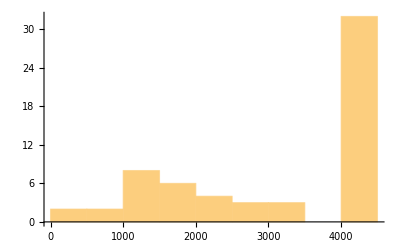

```mathematica
Histogram[tempHistoData,{500}]
```

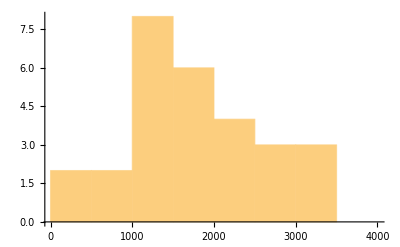

```mathematica
Histogram[Select[tempHistoData, #<4000&],{500},PlotRange->{{0,4000},All}]
```

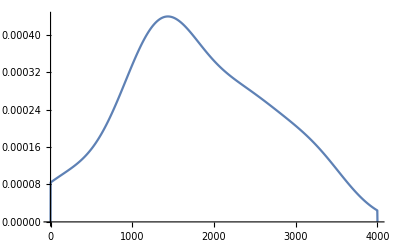

```mathematica
SmoothHistogram[Select[tempHistoData, #<4000&],PlotRange->{{0,4000},All}]
```

## Extracting trial latencies: PP2TrialEscapeLatency(*/PP2TrialResponseLatencyList*)

```mathematica
testDataTrials[[1]]
```

<|TrialNumber→1,STATEDATA→{{STATE,0,21,21,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,4925,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,51182,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,79973,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,99263,3,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,120476,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,144788,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,168337,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,180016,9,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{STATE,0,180093,77,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,0,181015,8,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,0,186082,65,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{STATE,0,187085,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,0,191295,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,203},{STATE,0,191307,12,1,14,FALSE,TRUE,FALSE,FALSE,484,0,203}},ERRORDATA→{{ERROR,99999,Run loop diff is >25 ms:    77},{ERROR,99999,Run loop diff is >25 ms:    65},{ERROR,99999,Run loop diff is >25 ms:    28}},TRIALDATA→{{TRIAL,1,1,1,600.,250.,4,2000.,4000.,0.,0.}}|>

```mathematica
(*This way, you only have to deal with one trial worth of state annotations at a time!*)
```

```mathematica
testDataTrials[[1, "STATEDATA"]]
```

{{STATE,0,21,21,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,4925,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,51182,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,79973,4,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,99263,3,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,120476,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,144788,4,2,1,FALSE,FALSE,FALSE,FALSE,528,0,0},{STATE,0,168337,3,2,1,FALSE,TRUE,FALSE,FALSE,532,0,0},{STATE,0,180016,9,2,2,FALSE,TRUE,FALSE,FALSE,548,0,0},{STATE,0,180093,77,1,3,FALSE,TRUE,FALSE,FALSE,308,0,0},{STATE,0,181015,8,1,3,FALSE,FALSE,FALSE,FALSE,304,0,0},{STATE,0,186082,65,1,4,FALSE,FALSE,FALSE,FALSE,320,0,0},{STATE,0,187085,3,1,5,FALSE,FALSE,TRUE,FALSE,338,0,0},{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0},{STATE,0,191295,6,1,14,FALSE,TRUE,TRUE,FALSE,486,0,203},{STATE,0,191307,12,1,14,FALSE,TRUE,FALSE,FALSE,484,0,203}}

```mathematica
SequenceCases[testDataTrials[[1, "STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{7,9}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{7,14,9,14}, state2],___ }
}
]
```

{{{STATE,0,191090,4,1,7,FALSE,FALSE,TRUE,TRUE,371,0,0},{STATE,0,191289,3,1,7,FALSE,TRUE,TRUE,TRUE,375,0,0}}}

```mathematica
(*Hit trial has no escape*)
SequenceCases[testDataTrials[[2, "STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{7,9}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{7,14,9,14}, state2],___ }
}
]
```

{}

### Paste together into real function

```mathematica
PP2TrialEscapeLatency[trialData_Association]:= 
Module[{tempret},
tempret=SequenceCases[trialData[["STATEDATA"]], 
{{"STATE",_,_,_,_,state1_/;MemberQ[{7,9}, state1],___ },
{"STATE",_,_,_,_,state2_/;MemberQ[{7,14,9,14}, state2],___ }
}
];
Switch[Length[tempret],
0, 0(*Null*),
1,tempret[[1, 2, 3]]-tempret[[1, 1, 3]],
_, Message[PP2TrialResponseLatency::trialError, trialData]
]
];
```

```mathematica
PP2TrialEscapeLatency::trialError="Something is wrong with this trial!";
```

```mathematica
PP2TrialEscapeLatency[x___]:= Message[PP2TrialEscapeLatency::invalidArgs, x];
```

### Tests

```mathematica
PP2TrialEscapeLatency[testDataTrials[[1]]]
```

199

```mathematica
PP2TrialEscapeLatency[testDataTrials[[3]]]
```

0

```mathematica
tempHistoData=PP2TrialEscapeLatency /@ testDataTrials
```

{199,0,0,0,0,0,0,0,0,3003,0,0,305,0,0,668,0,0,0,2605,0,0,0,6002,0,607,0,0,0,0,0,0,0,3028,0,0,5802,4175,0,364,0,0,2029,3321,0,758,440,4013,0,0,476,1227,0,0,0,0,571,0,0,2916}

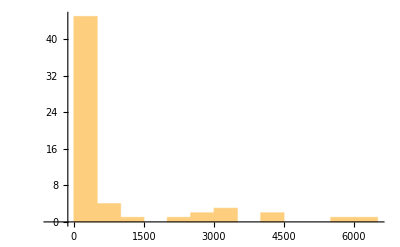

```mathematica
Histogram[tempHistoData,{500}]
```

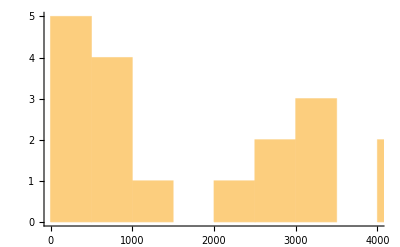

```mathematica
Histogram[Select[tempHistoData, 0<#&],{500},PlotRange->{{0,4000},All}]
```

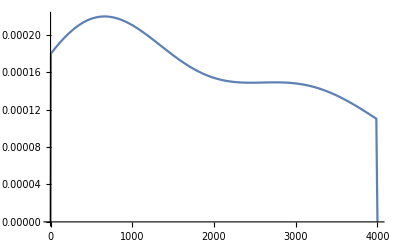

```mathematica
SmoothHistogram[Select[tempHistoData, 0<#&],PlotRange->{{0,4000},All}]
```

## Counting Up the Results

```mathematica
counts=Counts[PP2TrialExtractOutcome /@ testDataTrials ]
```

<|M→11,H→19,CR→21,FA→9|>

```mathematica
{N[counts[["H"]]/(counts[["H"]]+counts[["M"]])],N[counts[["FA"]]/(counts[["CR"]]+counts[["FA"]])]}
```

{0.633333,0.3}